C/C++ Sampler for Mathematica

Owen Scrambled Sobol

/home/max/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/randomRealOwen.so

LibraryFunction[…]

LibraryFunction[…]

0.179594

{0.179594,0.231584}

{0.319789,0.539257,0.249057,0.80511,0.4776,0.626624,0.0695488,0.915476,0.285555,0.587925,0.145465,0.861599,9976,0.479206,0.628228,0.0674628,0.916512,0.288192,0.587163,0.148224,0.859898,0.396856,0.710782,0.0617055,0.940656}
 |  |  |  |

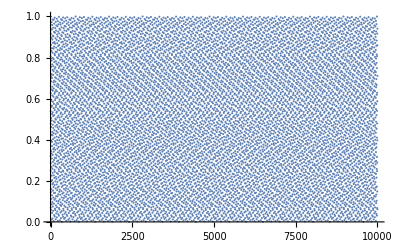

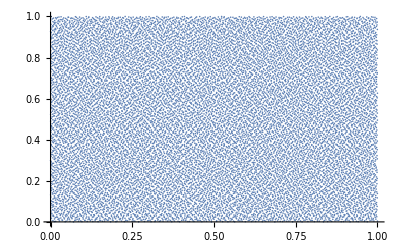

```mathematica
Needs["CCompilerDriver`"]
randomRealOwenLib=CreateLibrary[{"/home/max/git/Miscellaneous/MathematicaNotebooks/Samplers/C++/LibraryLink/randomRealOwen.cpp"},"randomRealOwen","Debug"->False, "CompileOptions"->"-O3"]
RandomRealOwen=LibraryFunctionLoad[randomRealOwenLib,"RandomRealOwen",{Integer},Real]
RandomRealOwen2D=LibraryFunctionLoad[randomRealOwenLib,"RandomRealOwen2D",{Integer},{Real,1}]

RandomRealOwen[123]
RandomRealOwen2D[123]

(* compare with RandomReal for speed *)
(*dd=Table[RandomRealOwen[i],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
dd=Table[RandomReal[],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]*)

(* 1D distibution *)
dd=Table[RandomRealOwen[i],{i,10^4}]
ListPlot[dd,ImageSize->Full]

(* 2D distibution *)
Clear[n,data];
n=8192*2;
data=ParallelTable[RandomRealOwen2D[i],{i,n}];
ListPlot[data,ImageSize->Full]
```

```mathematica
nextPowerOfTwo[ki_Integer]:=Module[{i=ki},
ca=ConstantArray[0,Length[IntegerDigits[i,2]]+1];
ca[[1]]=1;
FromDigits[ca,2]
];
convertSample[kx_]=2.0*kx-1.0;

Manipulate[
Module[{data,inside,insidepts},
(*data=RandomReal[{-1,1},{m,2}];*)
rdata=ParallelTable[ With[{i=i},RandomRealOwen2D[i]],{i,m}];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<=1];
inside=Length[insidepts];
Text@Style[Column[{
Graphics[{PointSize[0.005],RGBColor[0.25,0.76,0.19],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],
Row[{"Index: 1-",m,"\tN: ", t}],
Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],
Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],
            
{{m,256,"sample size"},64,8192,64,Appearance->"Labeled"},
{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

Halton

/home/max/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/randomRealHalton.so

LibraryFunction[…]

LibraryFunction[…]

0.829121

{0.0392456,0.703145}

{0.483689,0.0161583,0.599791,0.351478,0.523954,0.244855,0.323993,0.53277,0.267417,0.0954627,0.340645,0.0780357,9976,0.680827,0.661715,0.81793,0.505701,0.758227,0.609719,0.814575,0.424941,0.945642,0.878904,0.870489,0.146259}
 |  |  |  |

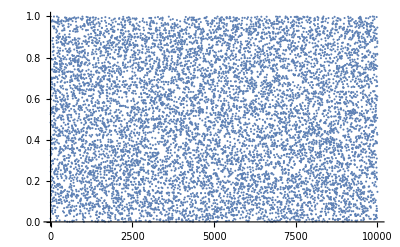

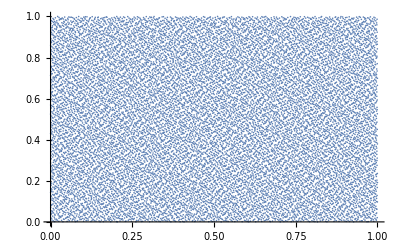

```mathematica
Needs["CCompilerDriver`"]
randomRealHaltonLib=CreateLibrary[{"/home/max/git/Miscellaneous/MathematicaNotebooks/Samplers/C++/LibraryLink/randomRealHalton.cpp"},"randomRealHalton","Debug"->False, "CompileOptions"->"-O3"]
RandomRealHalton=LibraryFunctionLoad[randomRealHaltonLib,"RandomRealHalton",{Integer},Real]
RandomRealHalton2D=LibraryFunctionLoad[randomRealHaltonLib,"RandomRealHalton2D",{Integer},{Real,1}]

RandomRealHalton[123688123]
RandomRealHalton2D[12368]

(* compare with RandomReal for speed *)
(*dd=Table[RandomRealHalton[i],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
dd=Table[RandomReal[],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
*)

(* 1D distibution *)
dd=Table[RandomRealHalton[i],{i,10^4}]
ListPlot[dd,ImageSize->Full]

(* 2D distibution *)
Clear[n,data];
n=8192*2;
data=ParallelTable[RandomRealHalton2D[i],{i,n}];
ListPlot[data,ImageSize->Full]
```

```mathematica
nextPowerOfTwo[ki_Integer]:=Module[{i=ki},
ca=ConstantArray[0,Length[IntegerDigits[i,2]]+1];
ca[[1]]=1;
FromDigits[ca,2]
];
convertSample[kx_]=2.0*kx-1.0;

Manipulate[
Module[{data,inside,insidepts},
(*data=RandomReal[{-1,1},{m,2}];*)
t=nextPowerOfTwo[m];
rdata=ParallelTable[ With[{i=i},RandomRealHalton2D[i]],{i,m}];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<=1];
inside=Length[insidepts];
Text@Style[Column[{
Graphics[{PointSize[0.005],RGBColor[0.25,0.76,0.19],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],
Row[{"Index: 1-",m,"\tN: ", t}],
Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],
Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],
            
{{m,256,"sample size"},64,8192,64,Appearance->"Labeled"},
{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

Correlated Multi-Jitter

/home/max/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/randomRealCMJ.so

LibraryFunction[…]

LibraryFunction[…]

0.314911

{0.579999,0.752401}

{0.643979,0.332504,0.268785,0.452042,0.579478,0.0107565,0.693116,0.834988,0.232818,0.708355,0.383035,0.152705,9976,0.324899,0.872454,0.722306,0.29742,0.947825,0.299437,0.223251,0.651746,0.678693,0.331474,0.510167,0.914139}
 |  |  |  |

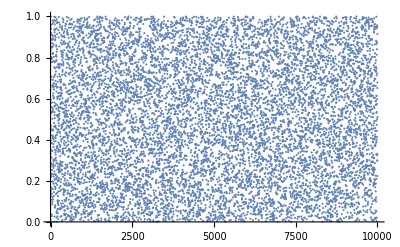

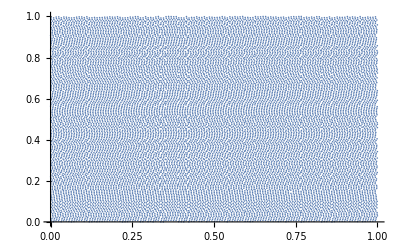

```mathematica
Needs["CCompilerDriver`"]
randomRealCMJLib=CreateLibrary[{"/home/max/git/Miscellaneous/MathematicaNotebooks/Samplers/C++/LibraryLink/randomRealCMJ.cpp"},"randomRealCMJ","Debug"->False, "CompileOptions"->"-O3"]
RandomRealCMJ=LibraryFunctionLoad[randomRealCMJLib,"RandomRealCMJ",{Integer},Real]
RandomRealCMJ2D=LibraryFunctionLoad[randomRealCMJLib,"RandomRealCMJ2D",{Integer,Integer},{Real,1}]

RandomRealCMJ[15]
RandomRealCMJ2D[15,24]

(* compare with RandomReal for speed *)
(*dd=Table[RandomRealCMJ[i],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
dd=Table[RandomReal[],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
*)

(* 1D distibution *)
dd=Table[RandomRealCMJ[i],{i,10^4}]
ListPlot[dd,ImageSize->Full]

(* 2D distibution *)
Clear[n,data];
n=8192*2;
data=ParallelTable[RandomRealCMJ2D[i,n],{i,n}];
ListPlot[data,ImageSize->Full]
```

```mathematica
nextPowerOfTwo[ki_Integer]:=Module[{i=ki},
ca=ConstantArray[0,Length[IntegerDigits[i,2]]+1];
ca[[1]]=1;
FromDigits[ca,2]
];
convertSample[kx_]=2.0*kx-1.0;

Manipulate[
Module[{data,inside,insidepts},
(*data=RandomReal[{-1,1},{m,2}];*)
t=nextPowerOfTwo[m];
rdata=ParallelTable[ With[{i=i},RandomRealCMJ2D[i,t]],{i,m}];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<=1];
inside=Length[insidepts];
Text@Style[Column[{
Graphics[{PointSize[0.005],RGBColor[0.25,0.76,0.19],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],
Row[{"Index: 1-",m,"\tN: ", t}],
Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],
Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],
            
{{m,256,"sample size"},64,8190,64,Appearance->"Labeled"},
{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

R2

/home/max/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/randomRealR2.so

LibraryFunction[…]

LibraryFunction[…]

0.856659

{0.856659,0.0903625}

{0.222343,0.592717,0.380233,0.123652,0.826691,0.646506,0.289668,0.0544171,0.897211,0.593434,0.371242,0.118935,0.848288,0.646099,9972,0.96582,0.720703,0.475098,0.228027,0.983887,0.73877,0.493164,0.249512,0.00537109,0.760254,0.51416,0.26709,0.0229492,0.77832}
 |  |  |  |

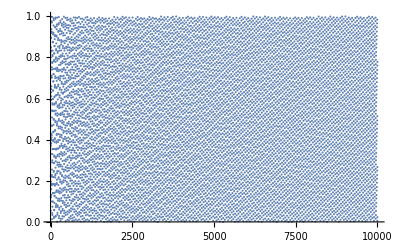

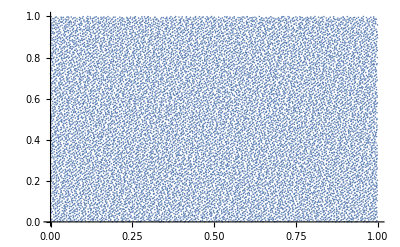

```mathematica
Needs["CCompilerDriver`"]
randomRealR2Lib=CreateLibrary[{"/home/max/git/Miscellaneous/MathematicaNotebooks/Samplers/C++/LibraryLink/randomRealR2.cpp"},"randomRealR2","Debug"->False, "CompileOptions"->"-O3"]
RandomRealR2=LibraryFunctionLoad[randomRealR2Lib,"RandomRealR2",{Integer},Real]
RandomRealR22D=LibraryFunctionLoad[randomRealR2Lib,"RandomRealR22D",{Integer},{Real,1}]

RandomRealR2[123]
RandomRealR22D[123]

(* compare with RandomReal for speed *)
(*dd=Table[RandomRealR2[i],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]
dd=Table[RandomReal[],{i,2*10^8}];//AbsoluteTiming
StandardDeviation[dd]*)

(* 1D distibution *)
dd=Table[RandomRealR2[i],{i,10^4}]
ListPlot[dd,ImageSize->Full]

(* 2D distibution *)
Clear[n,data];
n=8192*2;
data=ParallelTable[RandomRealR22D[i],{i,n}];
ListPlot[data,ImageSize->Full]
```

```mathematica
nextPowerOfTwo[ki_Integer]:=Module[{i=ki},
ca=ConstantArray[0,Length[IntegerDigits[i,2]]+1];
ca[[1]]=1;
FromDigits[ca,2]
];
convertSample[kx_]=2.0*kx-1.0;

Manipulate[
Module[{data,inside,insidepts},
(*data=RandomReal[{-1,1},{m,2}];*)
t=nextPowerOfTwo[m];
rdata=ParallelTable[ With[{i=i},RandomRealR22D[i]],{i,m}];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<=1];
inside=Length[insidepts];
Text@Style[Column[{
Graphics[{PointSize[0.005],RGBColor[0.25,0.76,0.19],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],
Row[{"Index: 1-",m,"\tN: ", t}],
Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],
Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],
            
{{m,256,"sample size"},64,8192,64,Appearance->"Labeled"},
{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

Low Discrepancy Blue Noise

```mathematica
Needs["CCompilerDriver`"]
randomRealLDBNLib=CreateLibrary[{"/home/max/git/Miscellaneous/MathematicaNotebooks/Samplers/C++/LibraryLink/randomRealLDBN.cpp"},"randomRealLDBN","Debug"->False, "CompileOptions"->"-O3"]
RandomRealLDBN=LibraryFunctionLoad[randomRealLDBNLib,"RandomRealLDBN",{Integer},{Real,1}]

RandomRealLDBN[14]
```

/home/max/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/randomRealLDBN.so

LibraryFunction[…]

{0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}